# An exploratory approach on a math problem

Kyungwon Chun
Sep. 16, 2019

```mathematica
<<SymbolicComputing`

boilerplateTemplate=StringTemplate["This notebook depends on Mathematica `ver` and MathSymbolica `scVer`. Also, the contents reflect the last execution on `date`."];
Print[boilerplateTemplate[<|"scVer"->$SCVersion,"ver"->$Version, "date"->DateString[]|>]]
```

This notebook depends on Mathematica 12.0.0 for Mac OS X x86 (64-bit) (April 7, 2019) and MathSymbolica 5.1.2 (July 22, 2019). Also, the contents reflect the last execution on Tue 24 Sep 2019 05:53:34.

## Problem

Find the lowest digit of Floor[10^20000/(10^100+3)].

## Solution

The number itself is really big.

```mathematica
Floor[10^20000/(10^100+3)]//IntegerLength
```

19900

Let’s plot each digits in order,

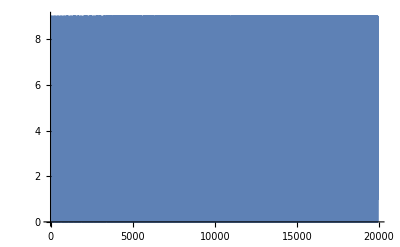

```mathematica
Floor[10^20000/(10^100+3)]//IntegerDigits//ListLinePlot
```

It seems that numbers are randomly distributed and cannot see any structure in it.

Try to zoom up to find some structure in it.

```mathematica
Manipulate[Module[{digitList=IntegerDigits@Floor[10^20000/(10^100+3)]},
ListLinePlot[Thread[{Range[s,e],Take[digitList,{s,e}]}],PlotRange->{0,9}]
],
{{s,1,"start"},1,e,100},{{e,19900,"end"},s,19900,100}]
```

We can find a pulse train structure at around the most significant digits. However, it becomes noisy, and at around the less significant digits, we hardly see the pattern.

The frequency of each number through whole digits is

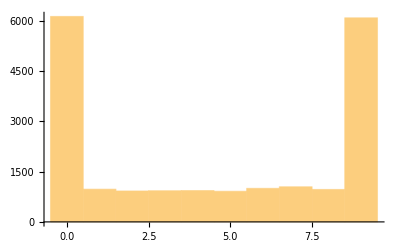

```mathematica
Floor[10^20000/(10^100+3)]//IntegerDigits//Histogram
```

There are dominant number of 0s and 9s.

For the upper half digits, this tendency is clear.

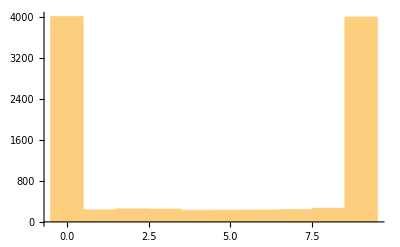

```mathematica
Floor[10^20000/(10^100+3)]//IntegerDigits//Take[#,19900/2]&//Histogram
```

The lower half digits also show this biased distribution, but, the tendency is less clear.

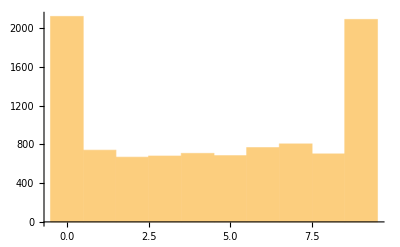

```mathematica
Floor[10^20000/(10^100+3)]//IntegerDigits//Take[#,-19900/2]&//Histogram
```

Though we investigated some aspect of this number, the number on the least significant digits is 3, contrary to our analysis.

```mathematica
Floor[10^20000/(10^100+3)]//IntegerDigits//Last
```

3